# Yukawa

```mathematica
NotebookDirectory[]
```

/home/raj/C_SM/ToySMat1Loop/

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
$model="Yukawa";
```

```mathematica
<<GenAmp`
```

Patched 2 FeynArts models.

## Setup

```mathematica
$gaugerules={FAGaugeXi[S[1]]:> 1};
```

```mathematica
$ampconfigFCFAConvert={ChangeDimension->D,Contract->False,DropSumOver->False,FCFADiracChainJoin->True,FeynAmpDenominatorCombine->True,
FinalSubstitutions->{},InitialSubstitutions->{},List->False,LoopMomenta->{l},LorentzIndexNames->{},Prefactor->1,SMP->False,SUNFIndexNames->{},
SUNIndexNames->{},TransversePolarizationVectors->{},UndoChiralSplittings->False};
```

## Tree Level (2->2)

```mathematica
(*DTPPPP=diag[0,{S[1],S[1]},{S[1],S[1]}];*)
```

```mathematica
(*AmpTPPPP=FCFAConvert[CreateFeynAmp[#,GaugeRules->{FAGaugeXi[S[1]]:> 1}],IncomingMomenta->{p1t,p2t},OutgoingMomenta->{k1t,k2t},ChangeDimension->4,List->False]&/@DTPPPP//Total*)
```

```mathematica
(*FCClearScalarProducts[];
SetMandelstam[s,t,u,p1t,p2t,-k1t,-k2t,mP,mP,mP,mP];*)
```

```mathematica
(*AmpT22SQEDSSSS1=FeynAmpDenominatorExplicit[AmpTPPPP]//FullSimplify*)
```

## Tadpoles (1->0)

## One Loop P->0

loading generic model file /home/raj/C_SM/ToySMat1Loop/models/Yukawa/Yukawa.gen

> $GenericMixing is OFF

generic model {./models/Yukawa/Yukawa} initialized

loading classes model file /home/raj/C_SM/ToySMat1Loop/models/Yukawa/Yukawa.mod

> 3 particles (incl. antiparticles) in 2 classes

> $CounterTerms are ON

> 3 vertices

> 6 counterterms of order 1

classes model {./models/Yukawa/Yukawa} initialized

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

in total: 2 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ab/0/bb.m, 0 diagrams

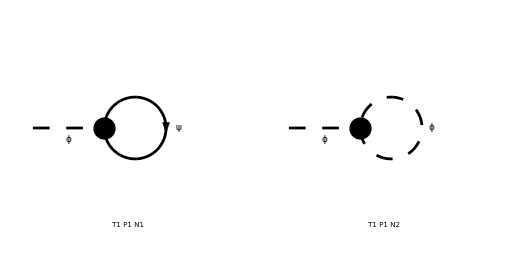

> Top. 1 ab/0/0.m, 0 diagrams

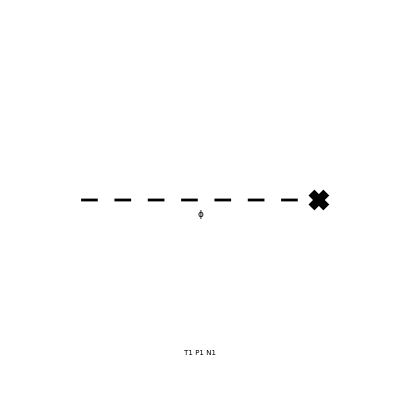

```mathematica
D1LP=diag[1,{S[1]},{}];
```

```mathematica
Amp1LP=D1LP//amp1L[{p1},{}]//DiracSimplify[#,DiracSubstitute67->True]&
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

Part::partw: Part 2 of {} does not exist.

{(ⅈ mF y)/(4 π^4 (l^2-mF^2))-(ⅈ g3)/(32 π^4 (l^2-mP^2)),-dv mP^2 √ZP}

```mathematica
Amp1LPDiv=Amp1LP//amp1LSimplify[{dv->Nd*dv,ZP-> 1+Nd*dP},{SMP["Delta"],dv,dP}]
```

(Δ (g3 mP^2-8 mF^3 y))/(16 π^2)-dv mP^2

```mathematica
dsol[0]=Solve[SelectFree2[Amp1LPDiv,p1]==0,dv]//Flatten//Simplify
dSave[dsol[0]];
```

{dv→(Δ (g3 mP^2-8 mF^3 y))/(16 π^2 mP^2)}

## One Loop F->0

```mathematica
D1LF=diag[1,{F[1]},{}];
```

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

in total: 0 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

in total: 0 Particles insertions

## One Loop (1->1)

## One Loop P->P

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

> Top. 2: 2 Particles insertions

in total: 3 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ac/bc/cc.m, 0 diagrams

> Top. 2 ac/bd/cdcd.m, 0 diagrams

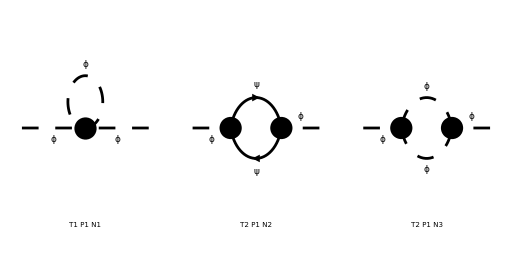

> Top. 1 ac/bc/0.m, 0 diagrams

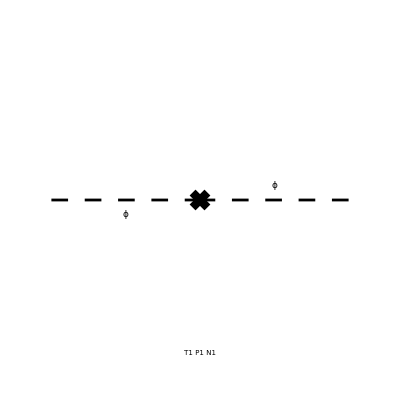

```mathematica
D1LPP=diag[1,{S[1]},{S[1]}];
```

```mathematica
Amp1LPP=D1LPP//amp1L[{p1},{p1}]//DiracSimplify[#,DiracSubstitute67->True]&
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 2 Particles amplitudes

in total: 3 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-(ⅈ g3^2)/(32 π^4 (l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ mF^2 y^2)/(4 π^4 (l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ l^2 y^2)/(4 π^4 (l^2-mF^2).((l-p1)^2-mF^2))-(ⅈ y^2 (l·p1))/(4 π^4 (l^2-mF^2).((l-p1)^2-mF^2))-(ⅈ mF^2 y5^2)/(4 π^4 (l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ l^2 y5^2)/(4 π^4 (l^2-mF^2).((l-p1)^2-mF^2))-(ⅈ y5^2 (l·p1))/(4 π^4 (l^2-mF^2).((l-p1)^2-mF^2))-(ⅈ g4)/(32 π^4 (l^2-mP^2)),-ⅈ (ⅈ p1^2 (ZP-1)-ⅈ (dv g3 ZP^2+mP^2 ZmP^2 ZP-mP^2))}

```mathematica
Amp1LPPDiv=Amp1LPP//amp1LSimplify[{ZP->1+Nd*dP,ZmP->1+Nd*dmP,dv-> Nd*dv},{SMP["Delta"],dmP,dP,dv}]
```

-2 dmP mP^2-dP mP^2+dP p1^2-dv g3+(Δ (g3^2+g4 mP^2-24 mF^2 y^2-8 mF^2 y5^2+4 p1^2 y^2+4 p1^2 y5^2))/(16 π^2)

```mathematica
dsol[1]=Solve[SelectNotFree2[Amp1LPPDiv/.dSub[dP],p1]==0,dP]//Flatten//Simplify
dSave[dsol[1]];
```

{dP→-(Δ (y^2+y5^2))/(4 π^2)}

```mathematica
dsol[2]=Solve[SelectFree2[Amp1LPPDiv/.dSub[dmP],p1]==0,dmP]//Flatten//Simplify
dSave[dsol[2]];
```

{dmP→(Δ (8 g3 mF^3 y+g4 mP^4-8 mF^2 mP^2 (3 y^2+y5^2)+4 mP^4 (y^2+y5^2)))/(32 π^2 mP^4)}

## One Loop F->F

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 1 Particles insertion

in total: 1 Particles insertion

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ac/bd/cdcd.m, 0 diagrams

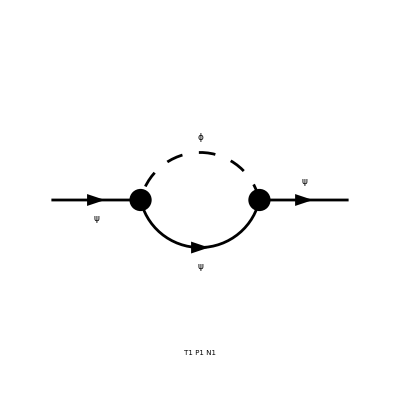

> Top. 1 ac/bc/0.m, 0 diagrams

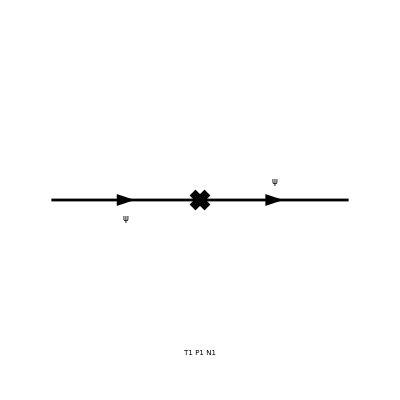

```mathematica
D1LFF=diag[1,{F[1]},{F[1]}];
```

```mathematica
Amp1LFF=D1LFF//amp1L[{p1},{p1}]//DiracSimplify[#,DiracSubstitute67->True]&
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{(mF y y5 (γ̄)^5)/(8 π^4 (l^2-mF^2).((l-p1)^2-mP^2))+-(ⅈ y^2 γ·l)/(16 π^4 (l^2-mF^2).((l-p1)^2-mP^2))-(ⅈ mF y^2)/(16 π^4 (l^2-mF^2).((l-p1)^2-mP^2))-(ⅈ y5^2 γ·l)/(16 π^4 (l^2-mF^2).((l-p1)^2-mP^2))+(ⅈ mF y5^2)/(16 π^4 (l^2-mF^2).((l-p1)^2-mP^2)),-ⅈ dCMA mF (γ̄)^5-ⅈ dv y5 (γ̄)^5-dv y+mF (-ZF) ZmF+mF-γ·p1+ZF γ·p1}

```mathematica
Amp1LFFDiv=Amp1LFF//amp1LSimplify[{ZF->1+Nd*dF,ZmF->1+Nd*dmF,dv-> Nd*dv,dCMA-> Nd*dCMA},{SMP["Delta"],dmF,dF,dv,dCMA}]
```

-ⅈ dCMA mF (γ̄)^5-ⅈ dv y5 (γ̄)^5+(Δ (4 ⅈ mF y y5 (γ̄)^5+2 mF y^2-2 mF y5^2+y^2 γ·p1+y5^2 γ·p1))/(16 π^2)-dF mF+dF γ·p1-dmF mF-dv y

```mathematica
dsol[3]=Solve[SelectNotFree2[Amp1LFFDiv/.dSub[dF],p1]==0,dF]//Flatten//Simplify
dSave[dsol[3]];
```

{dF→-(Δ (y^2+y5^2))/(16 π^2)}

```mathematica
dsol[4]=Solve[SelectFree2[Amp1LFFDiv/.dSub[dmF],{p1,DiracGamma[5]}]==0,dmF]//Flatten//Simplify
dSave[dsol[4]];
```

{dmF→-(Δ (g3 mP^2 y-8 mF^3 y^2+mF mP^2 (y5^2-3 y^2)))/(16 π^2 mF mP^2)}

```mathematica
dsol[5]=Solve[SelectNotFree2[Amp1LFFDiv/.dSub[dCMA],DiracGamma[5]]==0,dCMA]//Flatten//Simplify
dSave[dsol[5]];
```

{dCMA→(Δ y5 (4 mF y (2 mF^2+mP^2)-g3 mP^2))/(16 π^2 mF mP^2)}

## One Loop (2->1)

## One Loop PP->P

inserting at level(s) {Particles}

> Top. 1: 3 Particles insertions

> Top. 2: 1 Particles insertion

> Top. 3: 1 Particles insertion

> Top. 4: 1 Particles insertion

in total: 6 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 adbe/cf/dedfef.m, 0 diagrams

> Top. 2 adbe/ce/dede.m, 0 diagrams

> Top. 3 adbe/cd/eded.m, 0 diagrams

> Top. 4 adbd/ce/eded.m, 0 diagrams

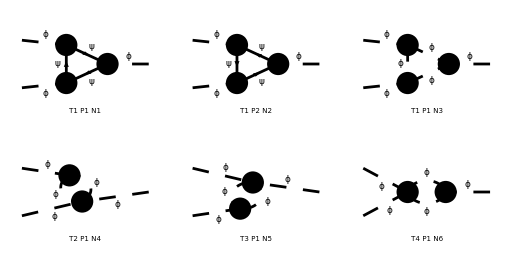

> Top. 1 adbd/cd/0.m, 0 diagrams

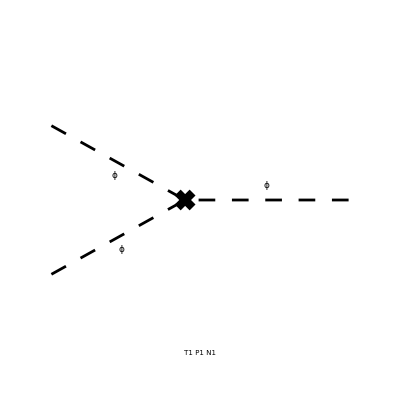

```mathematica
D1LPPP=diag[1,{S[1],S[1]},{S[1]}];
```

```mathematica
Amp1LPPP=D1LPPP//amp1L[{p1,p1},{2p1}]//DiracSimplify[#,DiracSubstitute67->True]&
```

creating amplitudes at level(s) {Particles}

> Top. 1: 3 Particles amplitudes

> Top. 2: 1 Particles amplitude

> Top. 3: 1 Particles amplitude

> Top. 4: 1 Particles amplitude

in total: 6 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-((ⅈ g3^3)/(16 π^4 (l^2-mP^2).((l+p1)^2-mP^2).((l-p1)^2-mP^2)))-(ⅈ g3 g4)/(16 π^4 (l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ g3 g4)/(32 π^4 (l^2-mP^2).((l+2 p1)^2-mP^2))+(3 ⅈ l^2 mF y^3)/(2 π^4 (l^2-mF^2).((l+p1)^2-mF^2).((l-p1)^2-mF^2))-(ⅈ mF p1^2 y^3)/(2 π^4 (l^2-mF^2).((l+p1)^2-mF^2).((l-p1)^2-mF^2))+(3 ⅈ l^2 mF y y5^2)/(2 π^4 (l^2-mF^2).((l+p1)^2-mF^2).((l-p1)^2-mF^2))-(ⅈ mF p1^2 y y5^2)/(2 π^4 (l^2-mF^2).((l+p1)^2-mF^2).((l-p1)^2-mF^2))+(ⅈ mF^3 y^3)/(2 π^4 (l^2-mF^2).((l+p1)^2-mF^2).((l-p1)^2-mF^2))-(3 ⅈ mF^3 y y5^2)/(2 π^4 (l^2-mF^2).((l+p1)^2-mF^2).((l-p1)^2-mF^2)),-dv g4 ZP^(3/2)-g3 Zg3 ZP^(3/2)+g3}

```mathematica
Amp1LPPPDiv=Amp1LPPP//amp1LSimplify[{ZP->1+Nd*dP,Zg3->1+Nd*dg3,dv-> Nd*dv},{SMP["Delta"],dP,dg3,dv}]
```

-dg3 g3-(3 dP g3)/2-dv g4+(3 Δ (g3 g4-16 mF y^3-16 mF y y5^2))/(16 π^2)

```mathematica
dsol[6]=Solve[SelectFree2[Amp1LPPPDiv/.dSub[dg3],p]==0,dg3]//Flatten//Simplify
dSave[dsol[6]];
```

{dg3→1/(8 π^2 g3 mP^2)Δ (g3 mP^2 (g4+3 (y^2+y5^2))+4 mF y (g4 mF^2-6 mP^2 (y^2+y5^2)))}

## One Loop FF->P

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

in total: 2 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 adbe/cf/dedfef.m, 0 diagrams

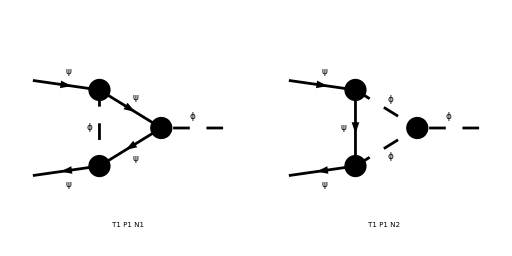

> Top. 1 adbd/cd/0.m, 0 diagrams

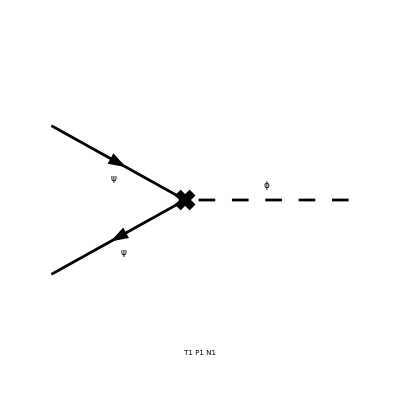

```mathematica
D1LFFP=diag[1,{F[1],-F[1]},{S[1]}];
```

```mathematica
Amp1LFFP=D1LFFP//amp1L[{p1,p1},{2p1}]//DiracSimplify[#,DiracSubstitute67->True]&
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{(ⅈ mF y^3 γ·l)/(8 π^4 (l^2-mP^2).((l+p1)^2-mF^2).((l-p1)^2-mF^2))+(ⅈ y^3 (γ·l).(γ·p1))/(16 π^4 (l^2-mP^2).((l+p1)^2-mF^2).((l-p1)^2-mF^2))-(ⅈ y^3 (γ·p1).(γ·l))/(16 π^4 (l^2-mP^2).((l+p1)^2-mF^2).((l-p1)^2-mF^2))-(ⅈ mF^2 y^3)/(16 π^4 (l^2-mP^2).((l+p1)^2-mF^2).((l-p1)^2-mF^2))-(ⅈ y^3 l^2)/(16 π^4 (l^2-mP^2).((l+p1)^2-mF^2).((l-p1)^2-mF^2))+(ⅈ y^3 p1^2)/(16 π^4 (l^2-mP^2).((l+p1)^2-mF^2).((l-p1)^2-mF^2))-(ⅈ g3 y^2 γ·l)/(16 π^4 (l^2-mF^2).((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ g3 mF y^2)/(16 π^4 (l^2-mF^2).((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(3 mF^2 y^2 y5 (γ̄)^5)/(16 π^4 (l^2-mP^2).((l+p1)^2-mF^2).((l-p1)^2-mF^2))-(mF y^2 y5 (γ·p1).(γ̄)^5)/(8 π^4 (l^2-mP^2).((l+p1)^2-mF^2).((l-p1)^2-mF^2))-(y^2 y5 (γ·l).(γ·p1).(γ̄)^5)/(16 π^4 (l^2-mP^2).((l+p1)^2-mF^2).((l-p1)^2-mF^2))+(y^2 y5 (γ·p1).(γ·l).(γ̄)^5)/(16 π^4 (l^2-mP^2).((l+p1)^2-mF^2).((l-p1)^2-mF^2))+(y^2 y5 (γ̄)^5 l^2)/(16 π^4 (l^2-mP^2).((l+p1)^2-mF^2).((l-p1)^2-mF^2))-(y^2 y5 (γ̄)^5 p1^2)/(16 π^4 (l^2-mP^2).((l+p1)^2-mF^2).((l-p1)^2-mF^2))+(g3 mF y y5 (γ̄)^5)/(8 π^4 (l^2-mF^2).((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(3 ⅈ mF^2 y y5^2)/(16 π^4 (l^2-mP^2).((l+p1)^2-mF^2).((l-p1)^2-mF^2))+(ⅈ mF y y5^2 γ·l)/(8 π^4 (l^2-mP^2).((l+p1)^2-mF^2).((l-p1)^2-mF^2))+(ⅈ y y5^2 (γ·l).(γ·p1))/(16 π^4 (l^2-mP^2).((l+p1)^2-mF^2).((l-p1)^2-mF^2))-(ⅈ y y5^2 (γ·p1).(γ·l))/(16 π^4 (l^2-mP^2).((l+p1)^2-mF^2).((l-p1)^2-mF^2))-(ⅈ y y5^2 l^2)/(16 π^4 (l^2-mP^2).((l+p1)^2-mF^2).((l-p1)^2-mF^2))+(ⅈ y y5^2 p1^2)/(16 π^4 (l^2-mP^2).((l+p1)^2-mF^2).((l-p1)^2-mF^2))+(ⅈ g3 mF y5^2)/(16 π^4 (l^2-mF^2).((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ g3 y5^2 γ·l)/(16 π^4 (l^2-mF^2).((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(mF^2 y5^3 (γ̄)^5)/(16 π^4 (l^2-mP^2).((l+p1)^2-mF^2).((l-p1)^2-mF^2))-(mF y5^3 (γ·p1).(γ̄)^5)/(8 π^4 (l^2-mP^2).((l+p1)^2-mF^2).((l-p1)^2-mF^2))-(y5^3 (γ·l).(γ·p1).(γ̄)^5)/(16 π^4 (l^2-mP^2).((l+p1)^2-mF^2).((l-p1)^2-mF^2))+(y5^3 (γ·p1).(γ·l).(γ̄)^5)/(16 π^4 (l^2-mP^2).((l+p1)^2-mF^2).((l-p1)^2-mF^2))+(y5^3 (γ̄)^5 l^2)/(16 π^4 (l^2-mP^2).((l+p1)^2-mF^2).((l-p1)^2-mF^2))-(y5^3 (γ̄)^5 p1^2)/(16 π^4 (l^2-mP^2).((l+p1)^2-mF^2).((l-p1)^2-mF^2)),-ZF √ZP Zy y-ⅈ dCMA (γ̄)^5 y+y+dCMA y5+ⅈ y5 (γ̄)^5-ⅈ y5 ZF √ZP Zy5 (γ̄)^5}

```mathematica
Amp1LFFPDiv=Amp1LFFP//amp1LSimplify[{ZF->1+Nd*dF,ZP->1+Nd*dP,Zy5->1+Nd*dy5,Zy->1+Nd*dy,dv-> Nd*dv,dCMA-> Nd*dCMA},{SMP["Delta"],dF,dP,dy5,dy,dv,dCMA}]
```

-ⅈ dCMA y (γ̄)^5-ⅈ dF y5 (γ̄)^5-1/2 ⅈ dP y5 (γ̄)^5-ⅈ dy5 y5 (γ̄)^5+(Δ (y-ⅈ y5) (y+ⅈ y5) (y+ⅈ y5 (γ̄)^5))/(8 π^2)+dCMA y5-dF y-(dP y)/2-dy y

```mathematica
dsol[7]=Simplify[Flatten[Solve[SelectFree2[Amp1LFFPDiv/.dSub[dy],DiracGamma[5]]==0,dy]]]
dSave[dsol[7]];
```

{dy→(Δ (-g3 mP^2 y5^2+8 mF^3 y y5^2+mF mP^2 y (5 y^2+9 y5^2)))/(16 π^2 mF mP^2 y)}

```mathematica
dsol[8]=Simplify[Flatten[Solve[SelectNotFree2[Amp1LFFPDiv/.dSub[dy5],DiracGamma[5]]==0,dy5]]]
dSave[dsol[8]];
```

{dy5→(Δ (g3 mP^2 y-8 mF^3 y^2+mF mP^2 (y^2+5 y5^2)))/(16 π^2 mF mP^2)}

## One Loop (2->2)

## One Loop PP->PP

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

> Top. 2: 1 Particles insertion

> Top. 3: 1 Particles insertion

> Top. 4: 1 Particles insertion

> Top. 5: 1 Particles insertion

> Top. 6: 1 Particles insertion

> Top. 7: 3 Particles insertions

> Top. 8: 3 Particles insertions

> Top. 9: 3 Particles insertions

> Top. 10: 1 Particles insertion

> Top. 11: 1 Particles insertion

> Top. 12: 1 Particles insertion

in total: 18 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 aebf/cgdg/efegfg.m, 0 diagrams

> Top. 2 aebf/cgdf/egefgf.m, 0 diagrams

> Top. 3 aebf/cfdg/egefgf.m, 0 diagrams

> Top. 4 aebf/cgde/fgfege.m, 0 diagrams

> Top. 5 aebf/cedg/fgfege.m, 0 diagrams

> Top. 6 aebe/cfdg/fgfege.m, 0 diagrams

> Top. 7 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 8 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 9 aebf/cgdh/egehfgfh.m, 0 diagrams

> Top. 10 aebe/cfdf/efef.m, 0 diagrams

> Top. 11 aebf/cedf/efef.m, 0 diagrams

> Top. 12 aebf/cfde/efef.m, 0 diagrams

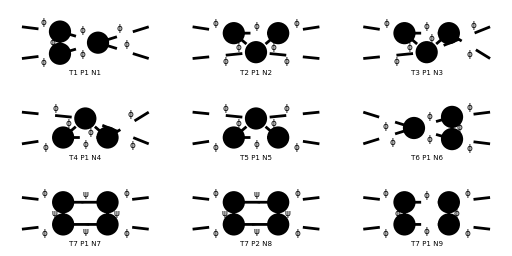

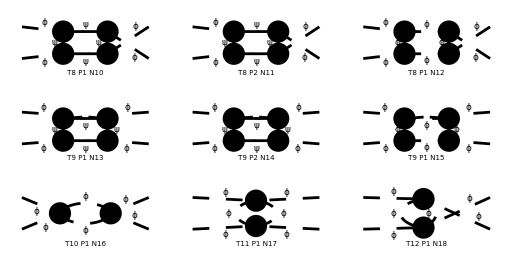

> Top. 1 aebe/cede/0.m, 0 diagrams

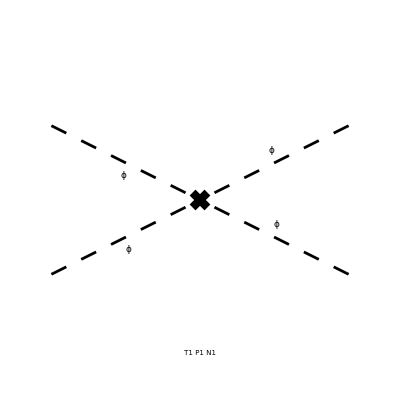

```mathematica
D1LPPPP=diag[1,{S[1],S[1]},{S[1],S[1]}];
```

```mathematica
Amp1LPPPP=D1LPPPP//amp1L[{p1,p1},{p1,p1}]//DiracSimplify[#,DiracSubstitute67->True]&
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

> Top. 3: 1 Particles amplitude

> Top. 4: 1 Particles amplitude

> Top. 5: 1 Particles amplitude

> Top. 6: 1 Particles amplitude

> Top. 7: 3 Particles amplitudes

> Top. 8: 3 Particles amplitudes

> Top. 9: 3 Particles amplitudes

> Top. 10: 1 Particles amplitude

> Top. 11: 1 Particles amplitude

> Top. 12: 1 Particles amplitude

in total: 18 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-(ⅈ g3^4)/(16 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ g3^4)/(8 π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ g3^2 g4)/(4 π^4 (l^2-mP^2).((l-p1)^2-mP^2)^2)-(ⅈ g3^2 g4)/(8 π^4 (l^2-mP^2).((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(ⅈ y^4 l^4)/(2 π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ y5^4 l^4)/(2 π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ y^2 y5^2 l^4)/(π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ y^4 l^4)/(π^4 (l^2-mF^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ y5^4 l^4)/(π^4 (l^2-mF^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(2 ⅈ y^2 y5^2 l^4)/(π^4 (l^2-mF^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ y^4 (l·p1)^2)/(π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ y5^4 (l·p1)^2)/(π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(2 ⅈ y^2 y5^2 (l·p1)^2)/(π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(2 ⅈ y^4 (l·p1)^2)/(π^4 (l^2-mF^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(2 ⅈ y5^4 (l·p1)^2)/(π^4 (l^2-mF^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(4 ⅈ y^2 y5^2 (l·p1)^2)/(π^4 (l^2-mF^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(ⅈ g4^2)/(16 π^4 (l^2-mP^2)^2)-(ⅈ g4^2)/(32 π^4 (l^2-mP^2).((l-2 p1)^2-mP^2))+(ⅈ mF^4 y^4)/(2 π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ mF^4 y5^4)/(2 π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(3 ⅈ mF^4 y^2 y5^2)/(π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ mF^4 y^4)/(π^4 (l^2-mF^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ mF^4 y5^4)/(π^4 (l^2-mF^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(6 ⅈ mF^4 y^2 y5^2)/(π^4 (l^2-mF^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(3 ⅈ mF^2 y^4 l^2)/(π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(ⅈ mF^2 y5^4 l^2)/(π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(2 ⅈ mF^2 y^2 y5^2 l^2)/(π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(6 ⅈ mF^2 y^4 l^2)/(π^4 (l^2-mF^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(2 ⅈ mF^2 y5^4 l^2)/(π^4 (l^2-mF^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(4 ⅈ mF^2 y^2 y5^2 l^2)/(π^4 (l^2-mF^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(3 ⅈ mF^2 y^4 (l·p1))/(π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ mF^2 y5^4 (l·p1))/(π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(2 ⅈ mF^2 y^2 y5^2 (l·p1))/(π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(ⅈ y^4 l^2 (l·p1))/(π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(ⅈ y5^4 l^2 (l·p1))/(π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(2 ⅈ y^2 y5^2 l^2 (l·p1))/(π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ mF^2 y^4 p1^2)/(2 π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ mF^2 y5^4 p1^2)/(2 π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ mF^2 y^2 y5^2 p1^2)/(π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(ⅈ mF^2 y^4 p1^2)/(π^4 (l^2-mF^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(ⅈ mF^2 y5^4 p1^2)/(π^4 (l^2-mF^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(2 ⅈ mF^2 y^2 y5^2 p1^2)/(π^4 (l^2-mF^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(ⅈ y^4 l^2 p1^2)/(2 π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(ⅈ y5^4 l^2 p1^2)/(2 π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(ⅈ y^2 y5^2 l^2 p1^2)/(π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ y^4 l^2 p1^2)/(π^4 (l^2-mF^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ y5^4 l^2 p1^2)/(π^4 (l^2-mF^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(2 ⅈ y^2 y5^2 l^2 p1^2)/(π^4 (l^2-mF^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2)),-g4 (Zg4 ZP^2-1)}

```mathematica
Amp1LPPPPDiv=Amp1LPPPP//amp1LSimplify[{ZP->1+Nd*dP,Zg4->1+Nd*dg4},{SMP["Delta"],dP,dg4}]
```

-dg4 g4-2 dP g4+(3 Δ (g4-4 y^2-4 y5^2) (g4+4 y^2+4 y5^2))/(16 π^2)

```mathematica
dsol[9]=Simplify[Flatten[Solve[SelectFree2[Amp1LPPPPDiv/.dSub[dg4],p]==0/.dsol[1],dg4]]]
dSave[dsol[9]];
```

{dg4→(Δ (3 g4^2+8 g4 (y^2+y5^2)-48 (y^2+y5^2)^2))/(16 π^2 g4)}

## One Loop FF->FF

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 1 Particles insertion

> Top. 8: 1 Particles insertion

> Top. 9: 2 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

in total: 4 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

in total: 0 Particles insertions

> Top. 1 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 2 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 3 aebf/cgdh/egehfgfh.m, 0 diagrams

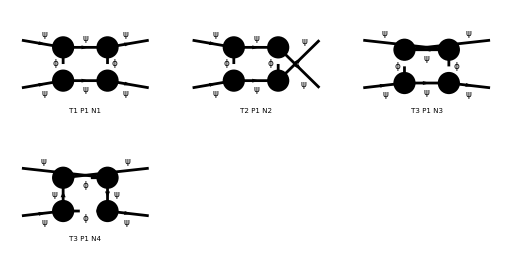

```mathematica
D1LFFFF=diag[1,{F[1],F[1]},{F[1],F[1]}];
```

```mathematica
Amp1LFFFF=D1LFFFF//amp1L[{p1,p1},{p1,p1}]//DiracSimplify[#,DiracSubstitute67->True]&
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

> Top. 3: 2 Particles amplitudes

in total: 4 Particles amplitudes

creating amplitudes at level(s) {Particles}

in total: 0 Particles amplitudes

{(ⅈ mF y^4 γ·l)/(8 π^4 (l^2-mF^2).((l-p1)^2-mP^2).(l^2-mF^2).((l-p1)^2-mP^2))+(ⅈ mF^2 y^4)/(16 π^4 (l^2-mF^2).((l-p1)^2-mP^2).(l^2-mF^2).((l-p1)^2-mP^2))+(ⅈ mF y^4 γ·l)/(8 π^4 (l^2-mP^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mF^2))-(ⅈ mF y^4 γ·p1)/(8 π^4 (l^2-mP^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mF^2))-(ⅈ mF^2 y^4)/(16 π^4 (l^2-mP^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mF^2))+(ⅈ y^4 l^2)/(16 π^4 (l^2-mF^2).((l-p1)^2-mP^2).(l^2-mF^2).((l-p1)^2-mP^2))-(ⅈ y^4 l^2)/(16 π^4 (l^2-mP^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mF^2))+(ⅈ y^4 (l·p1))/(8 π^4 (l^2-mP^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mF^2))-(ⅈ y^4 p1^2)/(16 π^4 (l^2-mP^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mF^2))-(mF^2 y^3 y5 (γ̄)^5)/(4 π^4 (l^2-mF^2).((l-p1)^2-mP^2).(l^2-mF^2).((l-p1)^2-mP^2))+(mF^2 y^3 y5 (γ̄)^5)/(4 π^4 (l^2-mP^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mF^2))-(3 ⅈ mF^2 y^2 y5^2)/(8 π^4 (l^2-mF^2).((l-p1)^2-mP^2).(l^2-mF^2).((l-p1)^2-mP^2))+(3 ⅈ mF^2 y^2 y5^2)/(8 π^4 (l^2-mP^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mF^2))+(ⅈ y^2 y5^2 l^2)/(8 π^4 (l^2-mF^2).((l-p1)^2-mP^2).(l^2-mF^2).((l-p1)^2-mP^2))-(ⅈ y^2 y5^2 l^2)/(8 π^4 (l^2-mP^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mF^2))+(ⅈ y^2 y5^2 (l·p1))/(4 π^4 (l^2-mP^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mF^2))-(ⅈ y^2 y5^2 p1^2)/(8 π^4 (l^2-mP^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mF^2))+(mF^2 y y5^3 (γ̄)^5)/(4 π^4 (l^2-mF^2).((l-p1)^2-mP^2).(l^2-mF^2).((l-p1)^2-mP^2))-(mF^2 y y5^3 (γ̄)^5)/(4 π^4 (l^2-mP^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mF^2))+(ⅈ mF^2 y5^4)/(16 π^4 (l^2-mF^2).((l-p1)^2-mP^2).(l^2-mF^2).((l-p1)^2-mP^2))-(ⅈ mF y5^4 γ·l)/(8 π^4 (l^2-mF^2).((l-p1)^2-mP^2).(l^2-mF^2).((l-p1)^2-mP^2))-(ⅈ mF^2 y5^4)/(16 π^4 (l^2-mP^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mF^2))-(ⅈ mF y5^4 γ·l)/(8 π^4 (l^2-mP^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mF^2))+(ⅈ mF y5^4 γ·p1)/(8 π^4 (l^2-mP^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mF^2))+(ⅈ y5^4 l^2)/(16 π^4 (l^2-mF^2).((l-p1)^2-mP^2).(l^2-mF^2).((l-p1)^2-mP^2))-(ⅈ y5^4 l^2)/(16 π^4 (l^2-mP^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mF^2))+(ⅈ y5^4 (l·p1))/(8 π^4 (l^2-mP^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mF^2))-(ⅈ y5^4 p1^2)/(16 π^4 (l^2-mP^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mF^2)),0}

```mathematica
Amp1LFFFFDiv=Amp1LFFFF//amp1LSimplify[{},{SMP["Delta"]}]
```

0

## One Loop FF->PP

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 2 Particles insertions

> Top. 8: 2 Particles insertions

> Top. 9: 2 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

in total: 7 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

in total: 0 Particles insertions

> Top. 1 aebf/cgdg/efegfg.m, 0 diagrams

> Top. 2 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 3 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 4 aebf/cgdh/egehfgfh.m, 0 diagrams

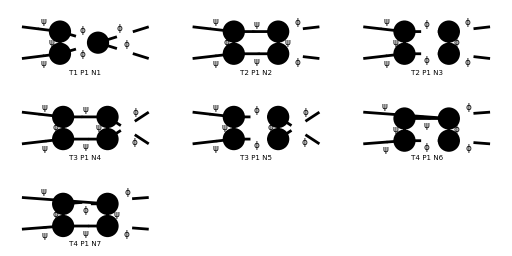

```mathematica
D1LFFPP=diag[1,{F[1],-F[1]},{S[1],S[1]}];
```

```mathematica
Amp1LFFPP=D1LFFPP//amp1L[{p1,p1},{p1,p1}]//DiracSimplify[#,DiracSubstitute67->True]&
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 2 Particles amplitudes

> Top. 3: 2 Particles amplitudes

> Top. 4: 2 Particles amplitudes

in total: 7 Particles amplitudes

creating amplitudes at level(s) {Particles}

in total: 0 Particles amplitudes

{(3 ⅈ mF^2 y^4 γ·l)/(8 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ mF y^4 (γ·l).(γ·p1))/(4 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(ⅈ mF y^4 (γ·p1).(γ·l))/(4 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(ⅈ mF^3 y^4)/(8 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ y^4 γ·l l^2)/(8 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(3 ⅈ mF y^4 l^2)/(8 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(ⅈ y^4 γ·p1 (l·p1))/(4 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ y^4 γ·l p1^2)/(8 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ mF y^4 p1^2)/(8 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(ⅈ g3 mF y^3 γ·l)/(8 π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ g3 mF y^3 γ·p1)/(16 π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ g3 y^3 (γ·p1).(γ·l))/(16 π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ g3 mF^2 y^3)/(16 π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ g3 mF y^3 γ·l)/(8 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mF^2).((l-p1)^2-mF^2))-(ⅈ g3 mF y^3 γ·p1)/(16 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ g3 y^3 (γ·l).(γ·p1))/(16 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mF^2).((l-p1)^2-mF^2))-(ⅈ g3 mF^2 y^3)/(16 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mF^2).((l-p1)^2-mF^2))+(mF^3 y^3 y5 (γ̄)^5)/(2 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(mF^2 y^3 y5 (γ·p1).(γ̄)^5)/(2 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(mF y^3 y5 (γ·l).(γ·p1).(γ̄)^5)/(4 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(mF y^3 y5 (γ·p1).(γ·l).(γ̄)^5)/(4 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(ⅈ g3 y^3 l^2)/(16 π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ g3 y^3 l^2)/(16 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mF^2).((l-p1)^2-mF^2))+(mF y^3 y5 (γ̄)^5 l^2)/(2 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(ⅈ g4 y^2 γ·l)/(16 π^4 (l^2-mF^2).((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ g4 mF y^2)/(16 π^4 (l^2-mF^2).((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(3 g3 mF^2 y^2 y5 (γ̄)^5)/(16 π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mP^2))-(g3 mF y^2 y5 (γ·p1).(γ̄)^5)/(16 π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mP^2))-(g3 y^2 y5 (γ·p1).(γ·l).(γ̄)^5)/(16 π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ g3^2 y^2 γ·l)/(8 π^4 (l^2-mF^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ g3^2 mF y^2)/(8 π^4 (l^2-mF^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(3 g3 mF^2 y^2 y5 (γ̄)^5)/(16 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mF^2).((l-p1)^2-mF^2))-(g3 mF y^2 y5 (γ·p1).(γ̄)^5)/(16 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mF^2).((l-p1)^2-mF^2))-(g3 y^2 y5 (γ·l).(γ·p1).(γ̄)^5)/(16 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mF^2).((l-p1)^2-mF^2))+(3 ⅈ mF^3 y^2 y5^2)/(4 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ mF^2 y^2 y5^2 γ·l)/(4 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ mF y^2 y5^2 (γ·l).(γ·p1))/(4 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(ⅈ mF y^2 y5^2 (γ·p1).(γ·l))/(4 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(g3 y^2 y5 (γ̄)^5 l^2)/(16 π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mP^2))+(g3 y^2 y5 (γ̄)^5 l^2)/(16 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mF^2).((l-p1)^2-mF^2))-(ⅈ mF y^2 y5^2 l^2)/(4 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ y^2 y5^2 γ·l l^2)/(4 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(ⅈ y^2 y5^2 γ·p1 (l·p1))/(2 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ mF y^2 y5^2 p1^2)/(4 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ y^2 y5^2 γ·l p1^2)/(4 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(g4 mF y y5 (γ̄)^5)/(8 π^4 (l^2-mF^2).((l+p1)^2-mP^2).((l-p1)^2-mP^2))+(3 ⅈ g3 mF^2 y y5^2)/(16 π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ g3 mF y y5^2 γ·l)/(8 π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ g3 mF y y5^2 γ·p1)/(16 π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ g3 y y5^2 (γ·p1).(γ·l))/(16 π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mP^2))+(g3^2 mF y y5 (γ̄)^5)/(4 π^4 (l^2-mF^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))+(3 ⅈ g3 mF^2 y y5^2)/(16 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ g3 mF y y5^2 γ·l)/(8 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mF^2).((l-p1)^2-mF^2))-(ⅈ g3 mF y y5^2 γ·p1)/(16 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ g3 y y5^2 (γ·l).(γ·p1))/(16 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mF^2).((l-p1)^2-mF^2))-(mF^3 y y5^3 (γ̄)^5)/(2 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(mF^2 y y5^3 (γ·p1).(γ̄)^5)/(2 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(mF y y5^3 (γ·l).(γ·p1).(γ̄)^5)/(4 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(mF y y5^3 (γ·p1).(γ·l).(γ̄)^5)/(4 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(ⅈ g3 y y5^2 l^2)/(16 π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ g3 y y5^2 l^2)/(16 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mF^2).((l-p1)^2-mF^2))+(mF y y5^3 (γ̄)^5 l^2)/(2 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ g4 mF y5^2)/(16 π^4 (l^2-mF^2).((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ g4 y5^2 γ·l)/(16 π^4 (l^2-mF^2).((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(g3 mF^2 y5^3 (γ̄)^5)/(16 π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mP^2))-(g3 mF y5^3 (γ·p1).(γ̄)^5)/(16 π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mP^2))-(g3 y5^3 (γ·p1).(γ·l).(γ̄)^5)/(16 π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mP^2))+(ⅈ g3^2 mF y5^2)/(8 π^4 (l^2-mF^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ g3^2 y5^2 γ·l)/(8 π^4 (l^2-mF^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(g3 mF^2 y5^3 (γ̄)^5)/(16 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mF^2).((l-p1)^2-mF^2))-(g3 mF y5^3 (γ·p1).(γ̄)^5)/(16 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mF^2).((l-p1)^2-mF^2))-(g3 y5^3 (γ·l).(γ·p1).(γ̄)^5)/(16 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mF^2).((l-p1)^2-mF^2))-(ⅈ mF^3 y5^4)/(8 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(ⅈ mF^2 y5^4 γ·l)/(8 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(g3 y5^3 (γ̄)^5 l^2)/(16 π^4 (l^2-mF^2).((l-p1)^2-mF^2).(l^2-mP^2).((l-p1)^2-mP^2))+(g3 y5^3 (γ̄)^5 l^2)/(16 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ mF y5^4 l^2)/(8 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ y5^4 γ·l l^2)/(8 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))-(ⅈ y5^4 γ·p1 (l·p1))/(4 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ mF y5^4 p1^2)/(8 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2))+(ⅈ y5^4 γ·l p1^2)/(8 π^4 (l^2-mP^2).((l+p1)^2-mF^2).(l^2-mF^2).((l-p1)^2-mF^2)),0}

```mathematica
Amp1LFFPPDiv=Amp1LFFPP//amp1LSimplify[{},{SMP["Delta"]}]
```

0

## Final answers

```mathematica
dvalues
```

{dv→(Δ (g3 mP^2-8 mF^3 y))/(16 π^2 mP^2),dP→-(Δ (y^2+y5^2))/(4 π^2),dmP→(Δ (8 g3 mF^3 y+g4 mP^4-8 mF^2 mP^2 (3 y^2+y5^2)+4 mP^4 (y^2+y5^2)))/(32 π^2 mP^4),dF→-(Δ (y^2+y5^2))/(16 π^2),dmF→-(Δ (g3 mP^2 y-8 mF^3 y^2+mF mP^2 (y5^2-3 y^2)))/(16 π^2 mF mP^2),dCMA→(Δ y5 (4 mF y (2 mF^2+mP^2)-g3 mP^2))/(16 π^2 mF mP^2),dg3→(Δ (g3 mP^2 (g4+3 (y^2+y5^2))+4 mF y (g4 mF^2-6 mP^2 (y^2+y5^2))))/(8 π^2 g3 mP^2),dy→(Δ (-g3 mP^2 y5^2+8 mF^3 y y5^2+mF mP^2 y (5 y^2+9 y5^2)))/(16 π^2 mF mP^2 y),dy5→(Δ (g3 mP^2 y-8 mF^3 y^2+mF mP^2 (y^2+5 y5^2)))/(16 π^2 mF mP^2),dg4→(Δ (3 g4^2+8 g4 (y^2+y5^2)-48 (y^2+y5^2)^2))/(16 π^2 g4)}